```mathematica
(* In this code block, I am trying to find the Fourier coefficients of the electric field .... *)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.6345×10^-8}. NIntegrate obtained 6.93889×10^-18 and 3.12496×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {0.202437}. NIntegrate obtained 3.60822×10^-16 and 1.96817×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.14159,3.60822×10^-16,0.0942572,3.88578×10^-16,0.157174,-6.93889×10^-17},«4»,{-0.0314159,-1.11022×10^-16,9.43043,3.60822×10^-16,-0.0157111,4.16334×10^-16}} may contain significant numerical errors.

b = {6.93889×10^-18,-9.54098×10^-18,9.75782×10^-18,0.,0.,0.}

A = (3.14159 | 3.60822×10^-16 | 0.0942572 | 3.88578×10^-16 | 0.157174 | -6.93889×10^-17
7.35523×10^-16 | 3.20505 | 1.83881×10^-16 | 1.73472×10^-16 | 4.89192×10^-16 | 0.193398
0.0314159 | 4.66641×10^-16 | 3.14348 | 8.32667×10^-16 | 0.00314222 | 4.49293×10^-16
3.14159 | -1.249×10^-16 | -0.282772 | 6.52256×10^-16 | 0.785869 | -2.79984×10^-15
-3.03577×10^-16 | 6.15878 | 5.6205×10^-16 | -3.53884×10^-16 | -7.28584×10^-16 | 1.10382
-0.0314159 | -1.11022×10^-16 | 9.43043 | 3.60822×10^-16 | -0.0157111 | 4.16334×10^-16) Dimensions = {6,6}

soln = {A1[1]→-1.37485×10^-18,A1[2]→6.01832×10^-18,A1[3]→5.52723×10^-19,A1[4]→-0.0138183,A1[5]→1.71639×10^-17,A1[6]→-3.80095×10^-17}

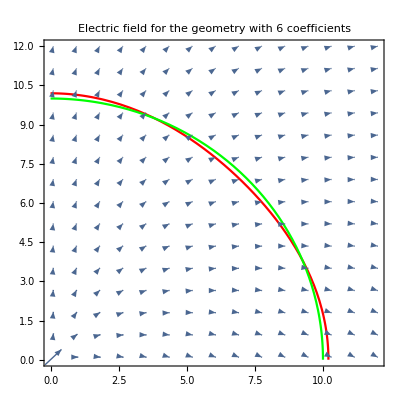

```mathematica
Block[
{R,λ,Er,Et,func,M,m,k,I1,I2,I3,A1,ϕ,eq1,eq2,eqn,var,soln,b,A,r,θ},
M=3; (* Half the number of coefficients *)
λ=0.02;(* The polar equation r = R(1+λcos4θ) *)
R=10;(* The range of the boundary curve *)
(* This block performs numerical integration ... *)
I1=<||>;I2=<||>;I3=<||>;
For[
k=1,k≤M,k++,
For[
m=1,m≤2M,m++,
I1=Append[I1,k->NIntegrate[Log[1+λ Cos[4θ]]Cos[k θ],{θ,-π,π}]];
I2=Append[I2,{m,k}->NIntegrate[(1+λ Cos[4θ])^m Cos[m θ]Cos[k θ],{θ,-π,π}]];
I3=Append[I3,{m,k}->NIntegrate[(1+λ Cos[4θ])^m Sin[m θ]Sin[k θ],{θ,-π,π}]];
]
];
eq1=Table[I1[k]+Sum[A1[m]I2[{m,k}],{m,1,2M}]==0,{k,1,M}];
eq2=Table[Sum[m A1[m]I3[{m,k}],{m,1,2M}]==0,{k,1,M}];
eqn=Join[eq1,eq2];
var=Table[A1[m],{m,1,2M}];
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
Print["b = ",b];
Print["A = ",MatrixForm[A]," Dimensions = ",Dimensions[A]];
soln=Table[var[[m]]->soln[[m]],{m,1,2M}];
Print["soln = ",soln];
Er[x_,y_]:=-(R/r+Total[Table[Part[(m A[m]Cos[m θ](r/R)^(m-1))/.soln,1],{m,1,2M}]])/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
Et[x_,y_]:=(Total[Table[Part[(m A[m]Cos[m θ](r/R)^(m-1))/.soln,1],{m,1,2M}]])/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
Show[VectorPlot[{-(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],-(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,1.2R},{y,0.01R,1.2R},VectorScale->{0.05,1,Automatic}],PolarPlot[R (1+λ Cos[4θ]),{θ,0,π/2},PlotStyle->Red],
PolarPlot[R ,{θ,0,π/2},PlotStyle->Green],
PlotRange->{{0,1.2R},{0,1.2R}},PlotLabel->StringJoin["Electric field for the geometry with ",ToString[2 M]," coefficients "]]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415925972447566019283762852398820663440970335500423971097916365}. NIntegrate obtained -6.07153×10^-18 and 7.66033×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.6345×10^-8}. NIntegrate obtained 7.21645×10^-16 and 1.48887×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.14159,7.21645×10^-16,0.235767,4.61436×10^-16,0.394172,-6.93889×10^-17,0.0414053,7.63278×10^-16,0.0713053,6.2797×10^-16},«8»,{0.0785398,1.76942×10^-16,«6»,6.4734,-1.73472×10^-15}} may contain significant numerical errors.

b = {-6.07153×10^-18,-4.11997×10^-17,7.37257×10^-18,0.157178,2.34188×10^-17,0.,0.,0.,0.,0.}

A = (3.14159 | 7.21645×10^-16 | 0.235767 | 4.61436×10^-16 | 0.394172 | -6.93889×10^-17 | 0.0414053 | 7.63278×10^-16 | 0.0713053 | 6.2797×10^-16
1.66533×10^-16 | 3.3026 | 6.52256×10^-16 | -1.17267×10^-15 | -2.22045×10^-16 | 0.503712 | 1.82146×10^-16 | 8.04912×10^-16 | 6.52256×10^-16 | 0.0953197
0.0785398 | 1.66533×10^-16 | 3.15337 | 1.80411×10^-16 | 0.0196595 | 2.77556×10^-17 | 0.554939 | 2.60209×10^-16 | 0.00414268 | 1.56125×10^-17
2.39392×10^-16 | -1.13451×10^-15 | 3.1225×10^-16 | 3.17695 | -3.60822×10^-16 | -5.41234×10^-16 | 5.68989×10^-16 | 0.63934 | 8.29198×10^-16 | -4.0766×10^-16
0.0785398 | 2.77556×10^-17 | 0.00589049 | 2.44596×10^-16 | 3.1809 | 6.38378×10^-16 | 0.00172128 | 6.48787×10^-16 | 0.719267 | 5.06539×10^-16
3.14159 | 6.93889×10^-18 | -0.7073 | 2.77556×10^-17 | 1.97086 | -1.81105×10^-15 | -0.289837 | 2.22045×10^-15 | 0.641748 | -1.66533×10^-15
-4.02456×10^-16 | 5.97688 | -2.18575×10^-16 | 4.16334×10^-16 | -6.93889×10^-17 | 2.66796 | 1.55431×10^-15 | -1.33227×10^-15 | -1.17094×10^-16 | 0.834614
-0.0785398 | 6.93889×10^-17 | 9.46012 | -1.05471×10^-15 | -0.0982975 | 2.28983×10^-16 | 3.88458 | -2.70617×10^-15 | -0.0372841 | 5.55112×10^-16
4.12864×10^-16 | -3.67761×10^-16 | 2.91434×10^-16 | 12.6135 | -4.94396×10^-16 | 1.47798×10^-15 | 1.14145×10^-15 | 5.0706 | 1.10849×10^-15 | -8.1532×10^-15
0.0785398 | 1.76942×10^-16 | -0.0176715 | 4.92661×10^-16 | 15.9045 | -1.73819×10^-15 | -0.012049 | 6.80012×10^-16 | 6.4734 | -1.73472×10^-15) Dimensions = {10,10}

soln = {A1[1]→-7.83831×10^-17,A1[2]→0.00623883,A1[3]→-6.26914×10^-17,A1[4]→-0.0990696,A1[5]→-1.59049×10^-16,A1[6]→-0.0821353,A1[7]→2.69377×10^-16,A1[8]→0.246443,A1[9]→4.09861×10^-16,A1[10]→0.217879}

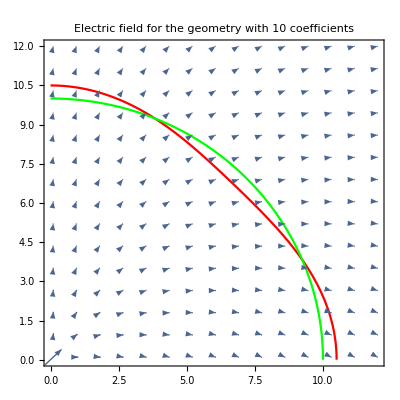

```mathematica
Block[
{R,λ,Er,Et,func,M,m,k,I1,I2,I3,A1,ϕ,eq1,eq2,eqn,var,soln,b,A,r,θ},
M=5; (* Half the number of coefficients *)
λ=0.05;(* The polar equation r = R(1+λcos4θ) *)
R=10;(* The range of the boundary curve *)
(* This block performs numerical integration ... *)
I1=<||>;I2=<||>;I3=<||>;
For[
k=1,k≤M,k++,
For[
m=1,m≤2M,m++,
I1=Append[I1,k->NIntegrate[Log[1+λ Cos[4θ]]Cos[k θ],{θ,-π,π}]];
I2=Append[I2,{m,k}->NIntegrate[(1+λ Cos[4θ])^m Cos[m θ]Cos[k θ],{θ,-π,π}]];
I3=Append[I3,{m,k}->NIntegrate[(1+λ Cos[4θ])^m Sin[m θ]Sin[k θ],{θ,-π,π}]];
]
];
eq1=Table[I1[k]+Sum[A1[m]I2[{m,k}],{m,1,2M}]==0,{k,1,M}];
eq2=Table[Sum[m A1[m]I3[{m,k}],{m,1,2M}]==0,{k,1,M}];
eqn=Join[eq1,eq2];
var=Table[A1[m],{m,1,2M}];
{b,A}=Normal[CoefficientArrays[eqn,var]];
soln=Inverse[A].(-b);
Print["b = ",b];
Print["A = ",MatrixForm[A]," Dimensions = ",Dimensions[A]];
soln=Table[var[[m]]->soln[[m]],{m,1,2M}];
Print["soln = ",soln];
Er[x_,y_]:=-(R/r+Total[Table[Part[(m A[m]Cos[m θ](r/R)^(m-1))/.soln,1],{m,1,2M}]])/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
Et[x_,y_]:=(Total[Table[Part[(m A[m]Cos[m θ](r/R)^(m-1))/.soln,1],{m,1,2M}]])/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]};
Show[VectorPlot[{-(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],-(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,1.2R},{y,0.01R,1.2R},VectorScale->{0.05,1,Automatic}],PolarPlot[R (1+λ Cos[4θ]),{θ,0,π/2},PlotStyle->Red],
PolarPlot[R ,{θ,0,π/2},PlotStyle->Green],
PlotRange->{{0,1.2R},{0,1.2R}},PlotLabel->StringJoin["Electric field for the geometry with ",ToString[2 M]," coefficients "]]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415925972447566019283762852398820663440970335500423971097916365}. NIntegrate obtained -6.07153×10^-18 and 7.66033×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.6345×10^-8}. NIntegrate obtained -4.11997×10^-17 and 8.0929×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.21486}. NIntegrate obtained 7.37257×10^-18 and 2.46538×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand Log[1+λ Cos[4 θ]] Sin[m θ] is being considered as zero over the specified region, but may actually be divergent.

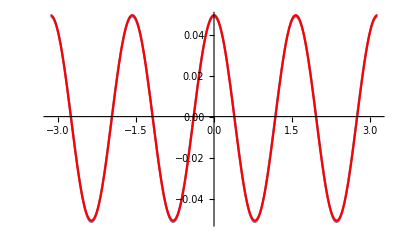

```mathematica
(* Here in this code fragment, I am trying compute and see the Fourier components of the function Log[1+λ Cos[4θ]] and regenerate the original function ... just to see if the convergence happens well*)
Block[
{A1,B1,M,λ},
λ=0.05;
M=5;
A1=Table[1/π NIntegrate[Log[1+λ Cos[4θ]]Cos[m θ],{θ,-π,π}],{m,0,M}];
B1=Table[1/π NIntegrate[Log[1+λ Cos[4θ]]Sin[m θ],{θ,-π,π}],{m,1,M}];
Show[
Plot[Log[1+λ Cos[4θ]],{θ,-π,π}],
Plot[A1[[1]]/2+Sum[A1[[m+1]]Cos[m θ]+B1[[m]]Sin[m θ],{m,1,M}],{θ,-π,π},PlotStyle->Red]
]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415925972447566019283762852398820663440970335500423971097916365}. NIntegrate obtained 1.0842×10^-19 and 1.57262×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.1415925972447566019283762852398820663440970335500423971097916365}. NIntegrate obtained 1.04083×10^-17 and 1.66337×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.93292}. NIntegrate obtained 2.81893×10^-18 and 2.1147×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

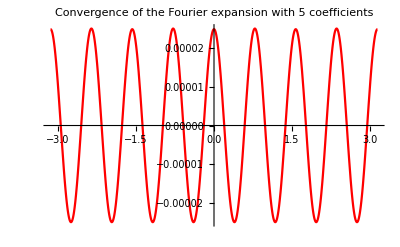

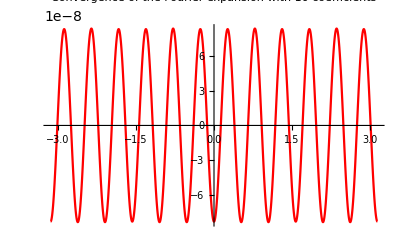

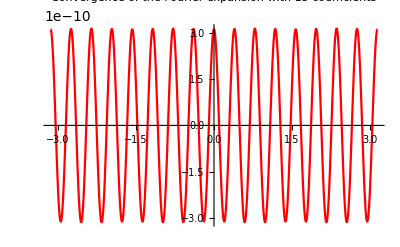

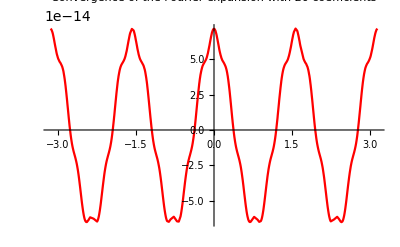

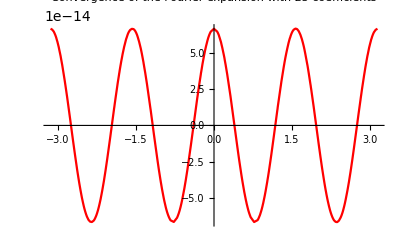

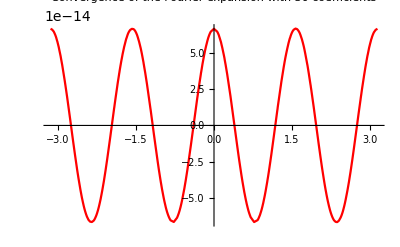

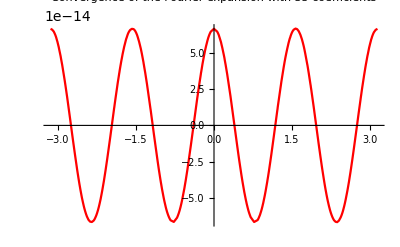

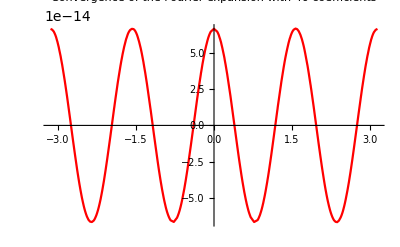

```mathematica
(* Here in this code fragment, I am seeing the difference between the original function and it's Fourier series expansion .... *)
Block[
{A1,B1,M,λ},
λ=0.01;
For[
M=5,M≤50,M=M+5,
A1=Table[1/π NIntegrate[Log[1+λ Cos[4θ]]Cos[m θ],{θ,-π,π}],{m,0,M}];
Print[Plot[A1[[1]]/2+Sum[A1[[m+1]]Cos[m θ],{m,1,M}]-Log[1+λ Cos[4θ]],{θ,-π,π},PlotStyle->Red,PlotLabel->"Convergence of the Fourier expansion with "<>ToString[M]<>" coefficients"]];
]
]
```

The value of the exponent g =10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.6345×10^-8}. NIntegrate obtained 8.46545×10^-16 and 1.58608×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.63824}. NIntegrate obtained -8.70831×10^-16 and 2.16442×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.84073}. NIntegrate obtained -1.9082×10^-16 and 3.63448×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

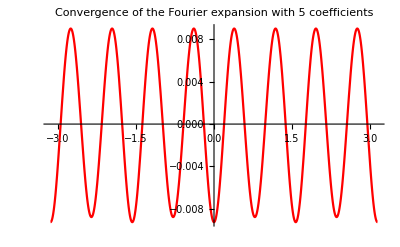

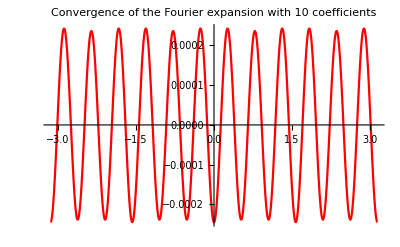

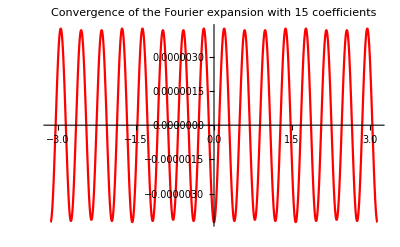

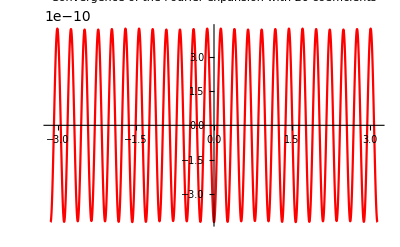

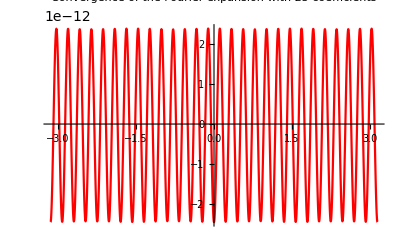

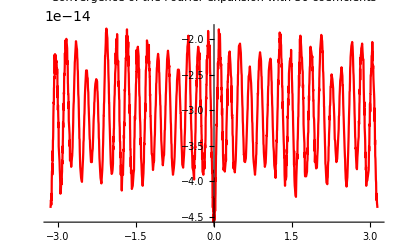

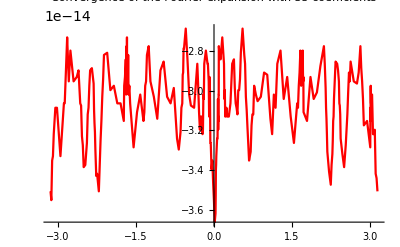

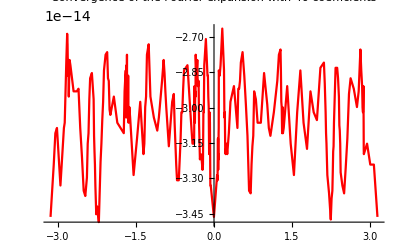

```mathematica
(* Here in this code fragment, I am repeating the same exercise with (1+λ Cos[4 θ])^g, g being some fixed integer .... *)
Block[
{A1,B1,M,λ,g},
λ=0.02;
g=RandomInteger[{6,14}];
Print["The value of the exponent g =",g];
For[
M=5,M≤50,M=M+5,
A1=Table[1/π NIntegrate[(1+λ Cos[4θ])^g Cos[m θ],{θ,-π,π}],{m,0,M}];
Print[Plot[A1[[1]]/2+Sum[A1[[m+1]]Cos[m θ],{m,1,M}]-(1+λ Cos[4θ])^g,{θ,-π,π},PlotStyle->Red,PlotLabel->"Convergence of the Fourier expansion with "<>ToString[M]<>" coefficients"]];
]
]
```

The value of the exponent g =14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.90209}. NIntegrate obtained -1.31405×10^-16 and 2.24931×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.28294×10^-8}. NIntegrate obtained -4.08007×10^-15 and 8.27278×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.6345×10^-8}. NIntegrate obtained 4.996×10^-16 and 1.59605×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

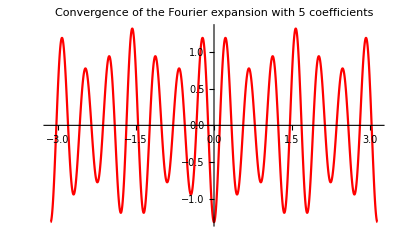

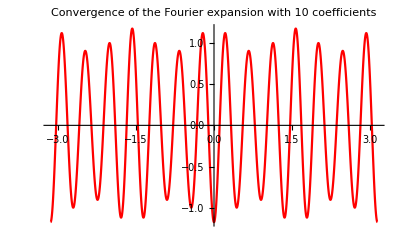

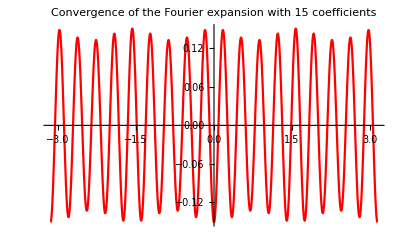

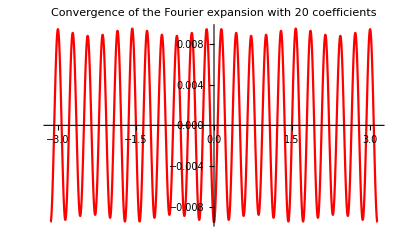

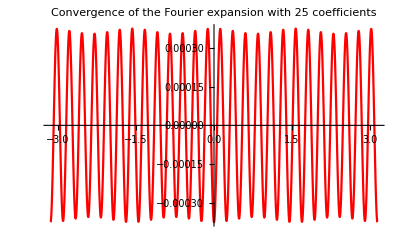

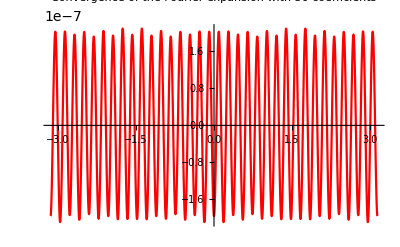

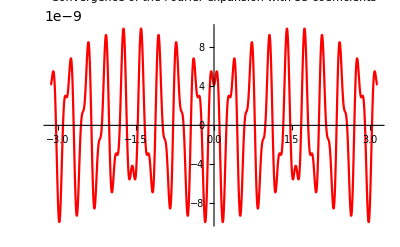

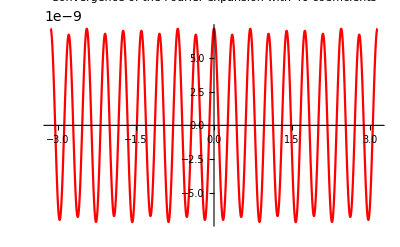

```mathematica
(* Here in this code fragment, I am repeating the same exercise with (1+λ Cos[4 θ])^g Cos[g θ], g being some fixed integer .... *)
Block[
{A1,B1,M,λ,g},
λ=0.02;
g=RandomInteger[{6,14}];
Print["The value of the exponent g =",g];
For[
M=5,M≤50,M=M+5,
A1=Table[1/π NIntegrate[(1+λ Cos[4θ])^g Cos[g θ]Cos[m θ],{θ,-π,π}],{m,0,M}];
Print[Plot[A1[[1]]/2+Sum[A1[[m+1]]Cos[m θ],{m,1,M}]-(1+λ Cos[4θ])^g Cos[g θ],{θ,-π,π},PlotStyle->Red,PlotLabel->"Convergence of the Fourier expansion with "<>ToString[M]<>" coefficients"]];
]
]
```

The value of the exponent g =6

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.49098}. NIntegrate obtained -4.66641×10^-16 and 2.14844×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.14071482607973028540644666595227363359299488365650177001953125}. NIntegrate obtained 6.93889×10^-17 and 4.59991×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.14071482607973028540644666595227363359299488365650177001953125}. NIntegrate obtained 4.44089×10^-16 and 3.12678×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

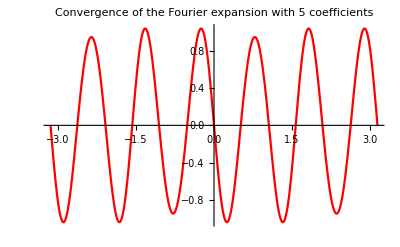

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

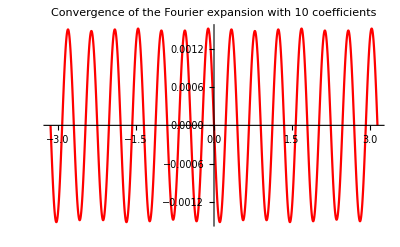

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

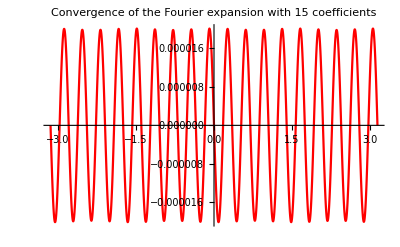

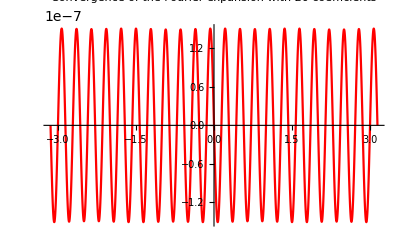

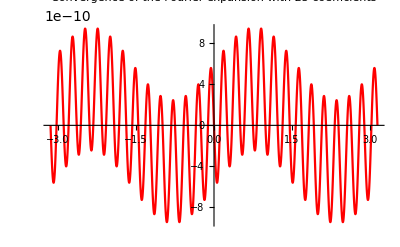

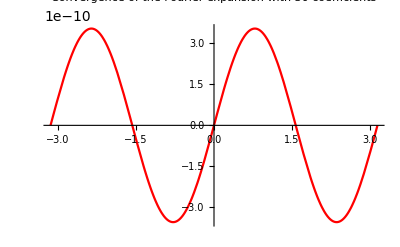

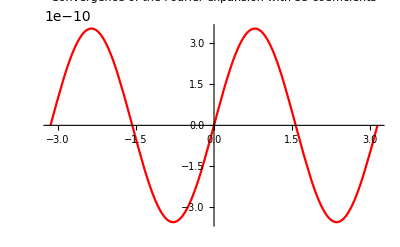

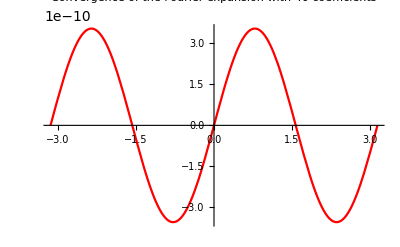

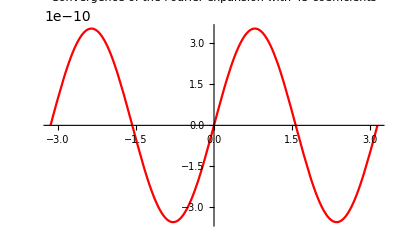

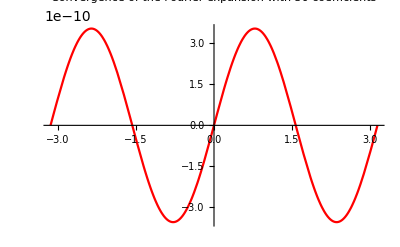

```mathematica
(* Here in this code fragment, I am repeating the same exercise with (1+λ Cos[4 θ])^g Sin[g θ], g being some fixed integer .... *)
Block[
{A1,B1,M,λ,g},
λ=0.02;
g=RandomInteger[{6,14}];
Print["The value of the exponent g =",g];
For[
M=5,M≤50,M=M+5,
A1=Table[1/π NIntegrate[(1+λ Cos[4θ])^g Sin[g θ]Sin[m θ],{θ,-π,π}],{m,0,M}];
Print[Plot[A1[[1]]/2+Sum[A1[[m+1]]Sin[m θ],{m,1,M}]-(1+λ Cos[4θ])^g Sin[g θ],{θ,-π,π},PlotStyle->Red,PlotLabel->"Convergence of the Fourier expansion with "<>ToString[M]<>" coefficients"]];
]
]
```